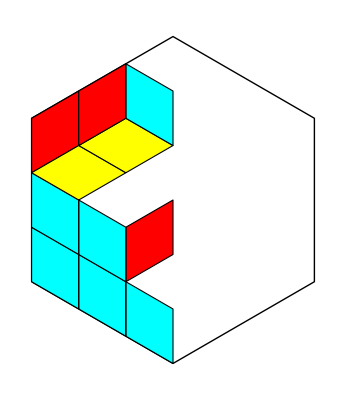

```mathematica
LozN = {Red,Parallelepiped[#1,{vN,{0,1}}]}&;
LozS = {Cyan,Parallelepiped[#1,{vS,{0,1}}]}&;
Loz0 = {Yellow,Parallelepiped[#1+{0,0},{vN,{-Sin[Pi/3],Cos[Pi/3]}}]}&;
Graphics[{Hexagon,EdgeForm[Black],
{LozS[{0,0}],LozS[{0,1}],LozN[{0,1}* 2]},
{Loz0[vN+{0,1}],Loz0[2vN+{0,1}]},
{LozS[vS],LozS[{0,1}+vS],LozN[{0,1}* 2+vN]},
{LozS[vS+vS],LozN[{0,1}+2vS],LozS[{0,1}* 2+2 vN]}
}]
```

```mathematica
Export["C:\\Users\\Bako\\Downloads\\PIXI\\images\\loz2s.png",Graphics[{EdgeForm[Black],LozS[{0,0}]},ImageSize->20, Background->None],Background->None]
```

C:\Users\Bako\Downloads\PIXI\images\loz2s.png

```mathematica
g = Graphics[{EdgeForm[Black],
{Loz0[2vN+{0,1}]},
{LozN[2vN]},
{LozS[{0,1}* 1+ vN]}
},ImageSize->40]
```

-Graphics-

```mathematica
Export["C:\\Users\\Bako\\Downloads\\PIXI\\images\\hex2.png",g,ImageSize->40,Background->None]
```

C:\Users\Bako\Downloads\PIXI\images\hex2.png